# Parallel Computing Exercise 3

## Marc Kassubeck (4054946) Torsten Thoben (4054959)

## Task 1a)

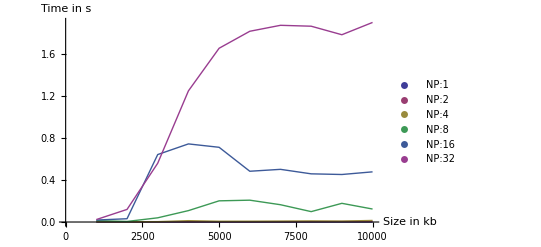

```mathematica
erg1=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01a_1_local.out"]);
erg2=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01a_2_local.out"]);
erg4=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01a_4_local.out"]);
erg8=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01a_8_local.out"]);
erg16=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01a_16_local.out"]);
erg32=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01a_32_local.out"]);
ListPlot[{erg1, erg2, erg4, erg8, erg16, erg32}, Joined->True, AxesLabel->{"Size in kb", "Time in s"}, PlotLegends->{"NP:1", "NP:2", "NP:4", "NP:8", "NP:16", "NP:32"}]
```

Caution: This Data does not represent runtimes from the cluster, as it was unavailable to us during the time for testing, thus, these are all locally taken results on a Core-i5 dual core CPU

Interesting here is the fact, that from a message size of circa 4000 kb onward the Broadcast time seems to stay constant.

## Task 1b)

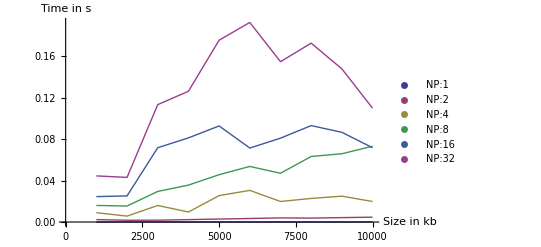

```mathematica
erg1=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01b_1_local.out"]);
erg2=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01b_2_local.out"]);
erg4=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01b_4_local.out"]);
erg8=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01b_8_local.out"]);
erg16=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01b_16_local.out"]);
erg32=ToExpression@StringDrop[#, -2]&/@(Drop[#, -1]&/@Import["ex01b_32_local.out"]);
ListPlot[{erg1, erg2, erg4, erg8, erg16, erg32}, Joined->True, AxesLabel->{"Size in kb", "Time in s"}, PlotLegends->{"NP:1", "NP:2", "NP:4", "NP:8", "NP:16", "NP:32"}]
```

Surprisingly local execution seems to be a lot faster than the broadcast-solution. Interesting is also, that the runtime seems to decrease for a high amount of processes and message sizes > 6000 kb.